```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts\\"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
bd[x_,a_,b_]=PDF[BetaDistribution[b,a],x]
```

Piecewise[{{((1-x)^(-1+a) x^(-1+b))/Beta[b,a], 0<x<1}, {0, True}}]

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
savedir="1gene-results_math2\\";
filename="gene";
allgenes=Range[1,94];
allsymptoms=Range[1,3];
symptomnames={"A","B","C"};
quantiles={0.05,0.95};
```

```mathematica
alnames={"A","B"};
gnames=Import["dataset1_binarized.csv"][[1,4+allgenes]];

qnames={"EV","STD","Q.05","Q.95","theta0","theta1","post.theta0","post.theta1"};
```

```mathematica
binoutcomes={0,1};
noutcomes=Length@binoutcomes;
alcombnames=alnames;
nalleles=Length@alnames;
ncombinations=Length@allgenes;
```

```mathematica
(* Calculate posterior theta parameters and resulting standard deviations and quantiles *)
ClearAll[logprob];
Do[Print[i];
sdata=data[[;;,Join[{i},3+allgenes]]];

Do[
f=Table[Count[Select[sdata,(#[[1+g1]]==x)&][[;;,1]],al],{al,{0,1}}
,{x,binoutcomes}];

logprob[t_]:=Block[{r2=f+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
noutcomes*(LogGamma[Total@t]-Total@LogGamma[t])];

theta={x,y}/.FindMaximum[{logprob[{x,y}],x>0,y>0},{{x,1},{y,1}}][[2]];

fnew=f+theta;
nnew=Total@fnew;
quantities={
(* EV *)
Flatten[T[T[fnew[[2;;]]]/nnew],1],
(* STD *)
Sqrt[(Times@@fnew)/(nnew^2*(1+nnew))],
(* Quantiles *)
Sequence@@(T@Table[Quantile[BetaDistribution[Sequence@@(Reverse[fnew[[;;,al]]])],quantiles],{al,binoutcomes+1}]),
(* Theta *)
Sequence@@(T@Table[theta,noutcomes]),
(* f + theta *)
Sequence@@fnew
};

csvquantities=Join[{Prepend[alnames,""]},T[Join[{qnames},T@quantities]]];

Export[savedir<>filename<>ToString[g1]<>"_s"<>symptomnames[[i]]<>".csv",csvquantities]
,{g1,allgenes}]
,{i,allsymptoms}]
```

```mathematica
(* Calculate various measures of "spread" *)
ClearAll[logprob];
Do[Print[i];
meanf=Mean[data[[;;,i]]];
spread=
Table[
values=Import[savedir<>filename<>ToString[g1]<>"_s"<>symptomnames[[i]]<>".csv"][[2,2;;]];
(*values=resu[[1]];*)
fmax=Max[values];
fmin=Min[values];drms=Sqrt[Mean[(values-meanf)^2]];
arms=Abs@Differences[values][[1]] (* only works for two-valued case *);
{g1,fmax,fmin,arms,drms}
,{g1,allgenes}];
Export["diffmeasures_1gene_s"<>symptomnames[[i]]<>".csv",Join[{{"gene1","max","min","spread","rms_mean"}},spread]];

,{i,allsymptoms}]
```

```mathematica
(* Make plots for alleles sorted by different measures of spread *)
```

```mathematica
datadir="1gene-results_math\\";data2[sy_,g1_]:=T[Import[datadir<>"gene"<>ToString[g1]<>"_s"<>symptomnames[[sy]]<>".csv"][[2;;,2;;]]];
```

```mathematica
ClearAll[spreads];
spreads[sy_]:=(thespread=Import["diffmeasures_1gene_s"<>symptomnames[[sy]]<>".csv"][[2;;,;;]];
thespread[[;;,3]]=-thespread[[;;,3]];
spreads[sy]=thespread);
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
geneseq=Import["dataset1_binarized.csv"][[1,5;;]];
geneseq=Table[ToString[i]<>" "<>geneseq[[i]],{i,Length@geneseq}];
```

```mathematica
numpairs=Length@allgenes;
sortcolumn=4 (* 2: fmax, 3: fmin, 4: fmax-fmin, 5: rms-dev *);
columnnames={"maxfr","minfr","spread","devrms","autorms"};
Do[
sortspreads=Sort[spreads[sym],(#1[[sortcolumn]]>#2[[sortcolumn]])&][[;;,1]];
data=Flatten[Table[data2[sym,Sequence@@sortspreads[[ii]]][[;;,1;;2]],{ii,numpairs}],1];

min=Min[data[[;;,1]]-data[[;;,2]]];
max=Max[data[[;;,1]]+data[[;;,2]]];

ticknames=Flatten@Table[{geneseq[[sortspreads[[ii]]]]<>"        "<>alnames[[1]],"        "<>alnames[[2]]},{ii,numpairs}];

plot=ErrorListPlot[data[[;;,{1,2}]],Joined->False,PlotRange->{min,max},Joined->False,AspectRatio->1/7,Frame->Auto,Axes->None,FrameLabel->{Style["gene",41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[numpairs*nalleles],Style[#,15]&/@(Rotate[#,Pi/2]&/@(ticknames))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{ArrayReshape[Riffle[Range[1/2,numpairs*nalleles+1/2,nalleles],Thick],{numpairs*nalleles+1,2}],Auto},ImageSize->a4longside*{5.5,1},Epilog->Text[Style["symptom "<>symptomnames[[sym]],42],Sequence@@labelposition[{0.5,0.99}]]];
Export["sort_"<>columnnames[[sortcolumn-1]]<>"_1gene_std_s"<>symptomnames[[sym]]<>".pdf",plot];
,{sym,3},{sortcolumn,Range[2,5]}]
```

```mathematica
resu=Import[savedir<>filename<>ToString[6]<>"_s"<>symptomnames[[1]]<>".csv"][[2;;,2;;]]
```

{{0.25917,0.283506},{0.00804727,0.00635616},{0.246026,0.2731},{0.272499,0.29401},{714.726,714.726},{266.147,266.147},{2195.73,3601.73},{768.147,1425.15}}

```mathematica
%//MF
```

(0.25917 | 0.283506
0.00804727 | 0.00635616
0.246026 | 0.2731
0.272499 | 0.29401
714.726 | 714.726
266.147 | 266.147
2195.73 | 3601.73
768.147 | 1425.15)

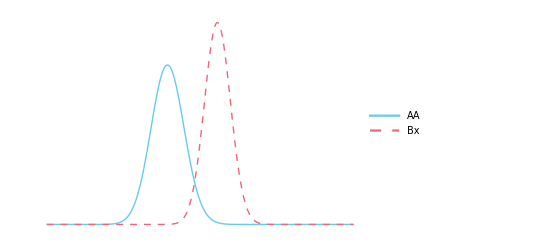

```mathematica
Plot[{bd[x,Sequence@@resu[[7;;8,1]]],bd[x,Sequence@@resu[[7;;8,2]]]},{x,0.2,0.35},PlotRange->All,Axes->None,Frame->Auto,FrameStyle->Directive[Large,Black],ImageSize->a5rsize,FrameLabel->{"frequency sympt. A, gene "<>geneseq[[6]],p[frequency | "data"]},PlotLegends->Placed[{"AA","Bx"},labelposition[{0.1,0.9}]]]
```

```mathematica
Export["example_distr_g6_sA.pdf",%]
```

example_distr_g6_sA.pdf

```mathematica
del=0.01;Total@Table[NIntegrate[bd[x,Sequence@@resu[[7;;8,1]]],{x,i,i+del}]*NIntegrate[bd[x,Sequence@@resu[[7;;8,2]]],{x,i,i+del}],{i,0,1-del,del}]
```

0.0321908

```mathematica
del=0.01;NIntegrate[bd[x,Sequence@@resu[[7;;8,1]]]*bd[y,Sequence@@resu[[7;;8,2]]],{x,0,1},{y,Max[0,x-del/2],Min[1,x+del/2]}]
```

0.0278337

```mathematica
checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,0,1}],1];
```

```mathematica
checkgenes=94;geneseq=Import["allcondfreqs_1gene_thetamax_sA.csv"][[1,2;;checkgenes*2+1]];
geneseq=Table[ToString[Ceiling[i/2]]<>" "<>geneseq[[i]],{i,Length@geneseq}];

symptomnames={"A","B","C"};allelenames={"A","B"};
```

```mathematica
(* save seq of results *)
ClearAll[checkdata2];
ii=0;Do[Print[sym];ii=ii+1;
datacf=T[Import["condcounts_s"<>sym<>".csv"][[2;;,2;;]]];

ClearAll[logprob,newtheta];
logprob[t_,g_]:=Block[{r2=g+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])];

newtheta[g_]:=Block[{fm,dat=datacf[[;;,{2*g-1,2*g}]]},
fm=({x,y}/.FindMaximum[{logprob[{x,y},dat],x>0,y>0},{{x,1},{y,1}}][[2]]);
Table[dat[[;;,ax]]+fm,{ax,2}]];

checkdata2[ii]=Table[
theta=newtheta[gx][[ax]];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,2}];
,{sym,symptomnames}]
```

```mathematica
Dimensions[checkdata2[1]]
```

{94,2,2}

```mathematica
checkdata2[1][[3]]
```

{{0.275632,0.00127375},{0.275273,0.00128111}}

```mathematica
checkdata[1][[;;10]]
```

{{0.270465,0.00582025},{0.290821,0.00861374},{0.275452,0.00171662},{0.27555,0.00170884},{0.275632,0.00127375},{0.275273,0.00128111},{0.275645,0.00175302},{0.275373,0.00175147},{0.275478,0.000943611},{0.275652,0.00095159}}

```mathematica
min=Min[checkdata[[;;,1]]-checkdata[[;;,2]]];
max=Max[checkdata[[;;,1]]+checkdata[[;;,2]]];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
ii=0;Do[Print[sym];ii=ii+1;

min=Min[Flatten[checkdata2[ii],1][[;;,1]]-Flatten[checkdata2[ii],1][[;;,2]]];
max=Max[Flatten[checkdata2[ii],1][[;;,1]]+Flatten[checkdata2[ii],1][[;;,2]]];

sortdata=SortBy[


checkdata[ii]=Table[
theta=newtheta[gx,ax];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,0,1}];(*rows: genes, cols: alleles, 3rd: mean+std *)

min=Min[checkdata[[;;,1]]-checkdata[[;;,2]]];
max=Max[checkdata[[;;,1]]+checkdata[[;;,2]]];plot=ErrorListPlot[checkdata[[;;,{1,2}]],PlotRange->{min,max},Joined->False,AspectRatio->1/7,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[checkgenes*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{Range[1/2,checkgenes*2+1/2,2],Auto},ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["1gene_std_s"<>sym<>".pdf",plot];,
{sym,symptomnames}]
```

```mathematica
(* with quantiles instead of std *)
Do[Print[sym];
datacf=T[Import["condcounts_s"<>sym<>".csv"][[2;;,2;;]]];
ClearAll[logprob,newtheta];
logprob[t_,g_]:=Block[{r2=datacf[[;;,{2*g-1,2*g}]]+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])];

newtheta[g_,i_]:=datacf[[;;,2*g-1+i]]+({x,y}/.FindMaximum[{logprob[{x,y},g],x>0,y>0},{{x,1},{y,1}}][[2]]);

checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{{gx*2-1+ax,theta[[2]]/tot},
ErrorBar[-theta[[2]]/tot+Quantile[BetaDistribution[theta[[2]],theta[[1]]],{0.05,0.95}]]},{gx,1,checkgenes},{ax,0,1}],1];

min=Min[checkdata[[;;,1,2]]+checkdata[[;;,2,1,1]]];
max=Max[checkdata[[;;,1,2]]+checkdata[[;;,2,1,2]]];plot=ErrorListPlot[checkdata[[;;,{1,2}]],PlotRange->{min,max},Joined->False,AspectRatio->1/6,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[checkgenes*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{Range[1/2,checkgenes*2+1/2,2],Auto},ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["mathematica_05quantile_s"<>sym<>".pdf",plot];,
{sym,symptomnames}]
```

```mathematica
a
```

a

```mathematica
oldtheta[3,1]
```

{1660,601}

```mathematica
newtheta[3,1]
```

{88092.5,33460.2}

```mathematica
bd[0.5,Sequence@@(newtheta[3,0])]
```

4.036684122×10^-5576

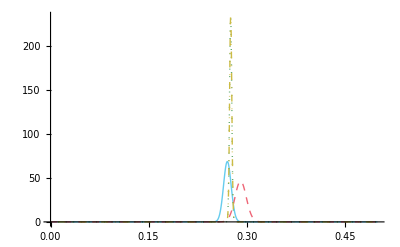

```mathematica
Plot[{bd[x,Sequence@@newtheta[1,0]],bd[x,Sequence@@newtheta[1,1]],bd[x,Sequence@@newtheta[2,0]],bd[x,Sequence@@newtheta[2,1]]},{x,0,0.5},PlotRange->All]
```